```mathematica
sss=Table[{w,x/.FindRoot[x==Sin[w*x],{x,3/4}]},{w,1,5,0.01}];
```

```mathematica
Dimensions[sss]
```

{401,2}

```mathematica
eigs=Table[{sss[[j]][[1]],Abs[sss[[j]][[1]]*Cos[sss[[j]][[1]]*sss[[j]][[2]]]]},{j,401}];
```

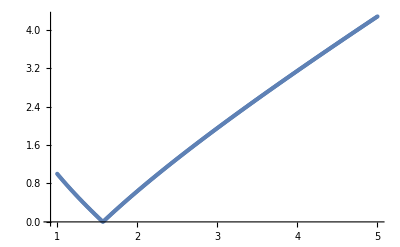

```mathematica
plt=ListPlot[eigs]
```

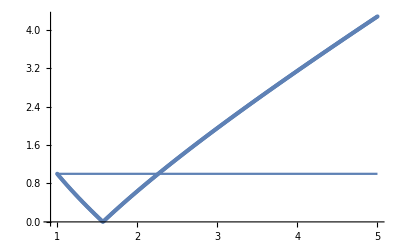

```mathematica
Show[plt,Plot[1,{x,1,5}]]
```

```mathematica
sol1=RecurrenceTable[{x[n+1]==Sin[3*x[n]/2],x[1]==0.01},x,{n,20}];
```

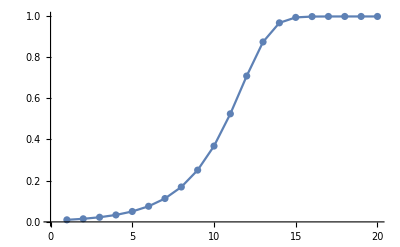

```mathematica
ListPlot[sol1,Joined->True,Mesh->All]
```

```mathematica
sol2=RecurrenceTable[{x[n+1]==Sin[8*x[n]/5],x[1]==0.01},x,{n,20}];
```

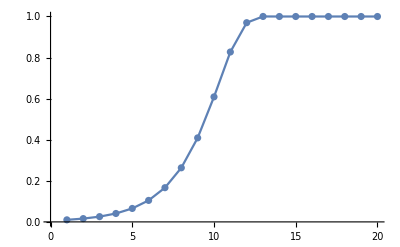

```mathematica
ListPlot[sol2,Joined->True,Mesh->All]
```

```mathematica
sol3=RecurrenceTable[{x[n+1]==Sin[2*x[n]],x[1]==0.01},x,{n,20}];
```

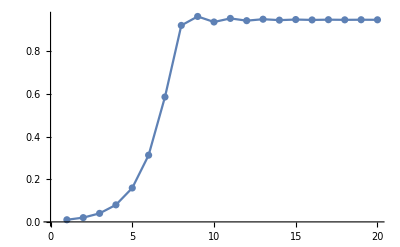

```mathematica
ListPlot[sol3,Joined->True,Mesh->All]
```

```mathematica
sol4=RecurrenceTable[{x[n+1]==Sin[11*x[n]/5],x[1]==0.01},x,{n,20}];
```

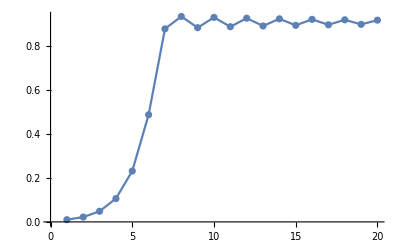

```mathematica
ListPlot[sol4,Joined->True,Mesh->All]
```

```mathematica
sol4=RecurrenceTable[{x[n+1]==Sin[12*x[n]/5],x[1]==0.01},x,{n,20}];
```

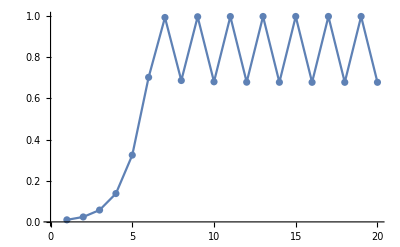

```mathematica
ListPlot[sol4,Joined->True,Mesh->All]
```

```mathematica
sol5=RecurrenceTable[{x[n+1]==Sin[7*x[n]/2],x[1]==0.01},x,{n,70}];
```

```mathematica
sol6=RecurrenceTable[{x[n+1]==Sin[7*x[n]/2],x[1]==0.0101},x,{n,70}];
```

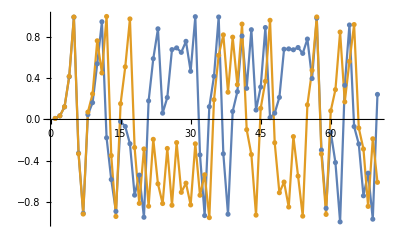

```mathematica
ListPlot[{sol5,sol6},Joined->True,Mesh->All]
```